```mathematica
h:=1/2f1 √(Jx Jy)Cos[ϕx-ϕy+2(δ s)/R]+(p Jx^2+r Jy^2)+f2 Jx Jy (2+Cos[2ϕx-2ϕy+4(δ s)/R])
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
input=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2v,f1->0,R->1,p->0,r->0,δ->δv,s->t});
```

```mathematica
Plot[(ϕx[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}])]
```

```mathematica
(ϕy[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]),{t,0,1000}],(((ϕx[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}])/.{t->50000})-(((ϕx[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}])/.{t->0})))/50000
```

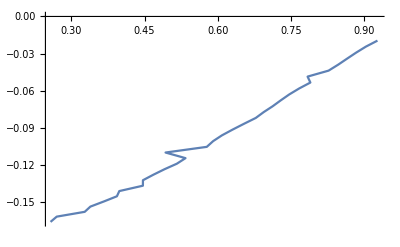

-0.230502+0.225601 x

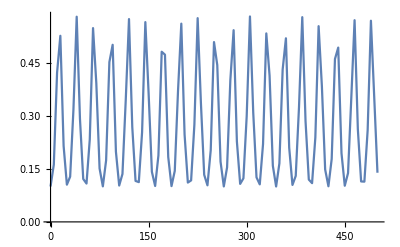

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.2};
ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000}]])/.{t->t1})],{t1,0,1000,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000}]])/.{t->1000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000}]])/.{t->0})))/1000},{Jxv1,0.1,0.9,.025}],Joined->True]
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.05}],{1,x},x]
ListPlot[Table[{t1,Abs[((Jx[t]/.Flatten[NDSolve[inloc/.{Jxv1->0.1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})]},{t1,0,500,5}],Joined->True]
```

```mathematica
0.046/0.03
```

1.53333

```mathematica
0.03 π/2
```

0.0471239

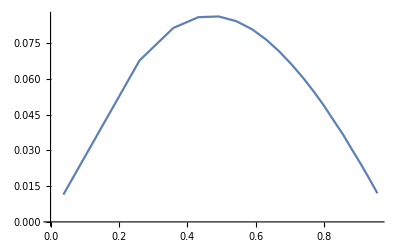

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.05};
a=ListPlot[Table[{Mean[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]},{Jxv1,0.001,0.901,.05}],Joined->True]
```

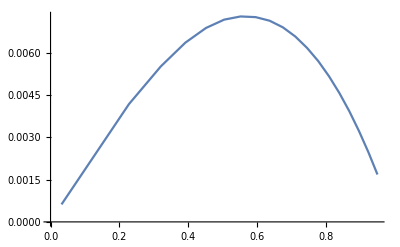

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.2,f2v->0.01};
a1=ListPlot[Table[{Mean[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]},{Jxv1,0.001,0.901,.05}],Joined->True]
```

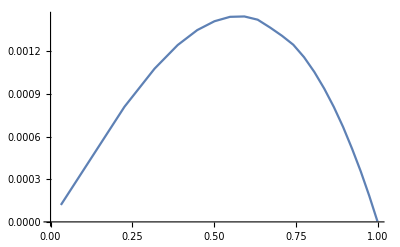

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.001};
a2=ListPlot[Table[{Mean[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]},{Jxv1,0.001,0.999,0.0499}],Joined->True]
```

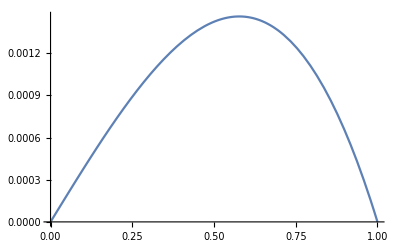

```mathematica
b=Plot[0.0038(x-x^3),{x,0,1}]
```

```mathematica
(0.999-0.001)/20
```

0.0499

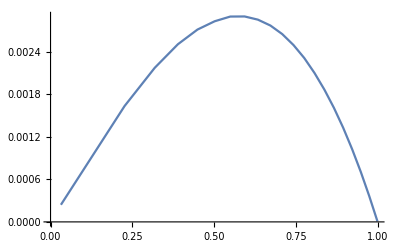

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.05,f2v->0.001};
an=ListPlot[Table[{Mean[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]},{Jxv1,0.001,0.999,0.0499}],Joined->True]
```

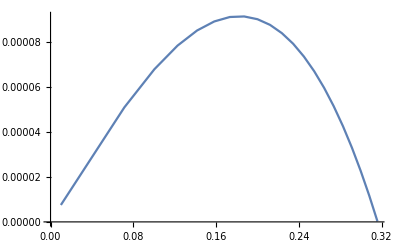

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.05,f2v->0.001};
an1=ListPlot[Table[{Mean[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]},{Jxv1,0.0001,0.0999,0.00499}],Joined->True]
```

```mathematica
1/N[Sqrt[10]]
```

0.316228

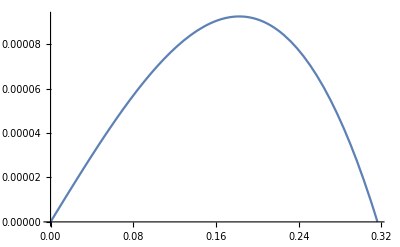

```mathematica
b2=Plot[2 0.0038/10(x-10x^3),{x,0,0.31622776601683794}]
```

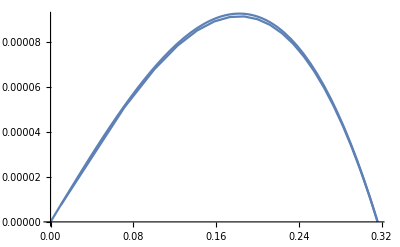

```mathematica
Show[{an1,b2}]
```

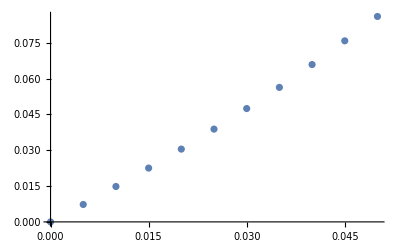

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->f2v1};
ListPlot[Table[{f2v1,Max[Table[Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],{Jxv1,0.001,0.999,0.0499}]]},{f2v1,0,0.05,0.005}]]
```

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.001};
a2=ListPlot[Table[{Mean[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]},{Jxv1,0.001,0.999,0.0499}],Joined->True]
```

-Graphics-

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.001};Max[Table[Max[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]]-Min[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],{Jxv1,0.001,0.999,0.0499}]]
```

0.00144501

```mathematica
N[3Sqrt[3]/20]
```

0.259808

```mathematica
N[Sqrt[2]]
```

1.41421

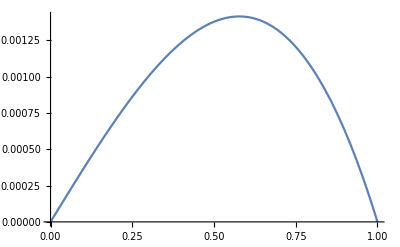

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.001};
bm=Plot[N[3Sqrt[6]/20]f2v x/δv (1-x^2)/.{δv->0.1,f2v->0.001},{x,0,1}]
```

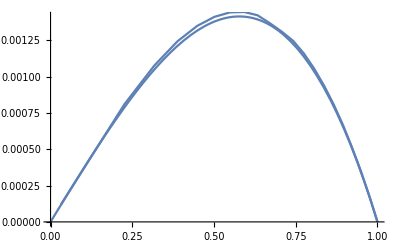

```mathematica
Show[{bm,a2}]
```

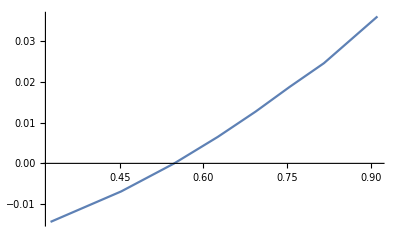

```mathematica
inloc=input/.{Jxv->Jxv1,Jyv->.3-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.06,f2v->0.05};
num=ListPlot[Table[{Mean[Table[Sqrt[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],Joined->True]
```

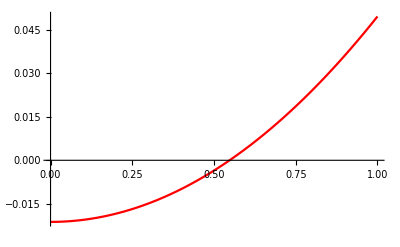

```mathematica
teor=Plot[(Sqrt[2]f2(x^2-II+ 27/1600f2^2 x^2 II ^2(1-x^2/II)^2/δ))/.{δ->0.06,f2->0.05,II->.3},{x,0,1},PlotStyle->Red]
```

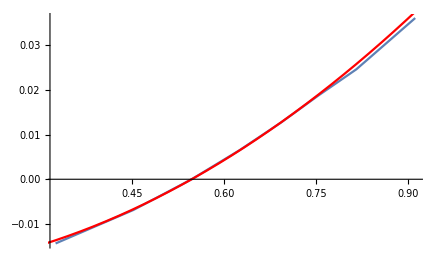

```mathematica
Show[{num,teor}]
```

```mathematica
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2v,f1->0,R->1,p->pv,r->rv,δ->δv,s->t});
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->pv1,rv->.1};
Table[Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x],{pv1,-.1,.1,.05}]
```

{-0.0152305-0.0597645 x,-0.0151901-0.0221706 x,-0.0150451+0.0151286 x,-0.0149148+0.0524573 x,-0.0150607+0.0901641 x}

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->f2v,pv->pv1,rv->.1};
Table[Fit[Table[{pv1,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->10000}},{pv1,-.1,.1,.05}],{1,x},x],{f2v,0,.01,0.001}]
```

{-3.26341×10^-19+0.75 x,0.00149524+0.750057 x,0.00298832+0.750215 x,0.00449382+0.750356 x,0.00601696+0.75038 x,0.00754934+0.750299 x,0.00907995+0.750225 x,0.0106061+0.750218 x,0.0121306+0.75013 x,0.0136514+0.74973 x,0.0151615+0.74897 x}

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->f2v,rv->rv1,pv->0};
Table[Fit[Table[{rv1,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->10000}},{rv1,-.1,.1,.05}],{1,x},x],{f2v,0,.01,0.001}]
```

{0.,0.00150121+9.73528×10^-6 x,0.0030065+0.000054012 x,0.00451479+0.0000747454 x,0.00602343+0.0000294848 x,0.00753169-0.0000343498 x,0.00904244-0.0000253599 x,0.0105586+0.0000719017 x,0.0120797+0.000184983 x,0.0136032+0.000267806 x,0.0151282+0.00036581 x}

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.01,rv->rv1,pv->.1};
Table[{rv1,Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x]},{rv1,-.1,.1,.05}]
```

{{-0.1,-0.015029+0.0901065 x},{-0.05,-0.0149511+0.0900561 x},{0.,-0.0149995+0.0901113 x},{0.05,-0.0150255+0.0900992 x},{0.1,-0.0150607+0.0901641 x}}

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.01,rv->rv,pv->.1};
Manipulate[ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc/.{rv->rv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,10}]],(((ϕx[t]/.Flatten[NDSolve[inloc/.{rv->rv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{rv->rv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}]],{rv1,-.1,.1,.05}]
```

NDSolve::deqn: Equation or list of equations expected instead of inloc in the first argument inloc.

ReplaceAll::reps: {NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[inloc,{Jx[0],ϕx[0],Jy[0],ϕy[0]},{0,0,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of inloc in the first argument inloc.

ReplaceAll::reps: {NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 10 cannot be used as a variable.

NDSolve::deqn: Equation or list of equations expected instead of inloc in the first argument inloc.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

NDSolve::dsvar: 20 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.